## Investigate the Zero Energy Edge State

Inspired by lecture by Kane of Topological Insulators (BSS 2016), I will analyse the continnum limit of this model at the  point (px=0,py=0), where the energy E=0. At this point Sin(p_x)→ p_x, and is replaced by -ⅈℏ∂_x. The Schrodinger equation is Hψ=0
After the calculation, the equation is:

```mathematica
[ⅈ D[σ^x, x]+ⅈ D[σ^y, y]+mσ^z]ψ=0
```

Now solve it using Mathematica:

```mathematica
DSolve[
{ⅈ*D[Psi2[x,y],x]+D[Psi2[x,y],y]+m*Psi1[x,y]==0,
ⅈ*D[Psi1[x,y],x]-D[Psi1[x,y],y]-m*Psi2[x,y]==0},
{Psi1[x,y],Psi2[x,y]},{x,y}]
```

DSolve[{m Psi1[x,y]+Psi2^(0,1)[x,y]+ⅈ Psi2^(1,0)[x,y]==0,-m Psi2[x,y]-Psi1^(0,1)[x,y]+ⅈ Psi1^(1,0)[x,y]==0},{Psi1[x,y],Psi2[x,y]},{x,y}]

Clearly, Mathematica does not how how to solve it analytically.

Then, I tried to decouple it. Assuming m(x,y)≠0, I replace for example Psi2 in the second line, using the firstline. I have:

```mathematica
eqq= {ⅈ*(-1/(m[x,y])^2(D[m[x,y], x])*(i D[Psi1[x,y], x]-D[Psi1[x,y], y])+1/m[x,y](ⅈ D[Psi1[x,y],{x,2}]-D[Psi1[x,y],y,x]))
+(-1/(m[x,y])^2(D[m[x,y], y])*(i D[Psi1[x,y], x]-D[Psi1[x,y], y])+1/m[x,y](ⅈ D[Psi1[x,y],x,y]-D[Psi1[x,y],{y,2}]))
+m[x,y] Psi1[x,y]==0}
```

{m[x,y] Psi1[x,y]-(m^(0,1)[x,y] (-Psi1^(0,1)[x,y]+i Psi1^(1,0)[x,y]))/m[x,y]^2+(-Psi1^(0,2)[x,y]+ⅈ Psi1^(1,1)[x,y])/m[x,y]+ⅈ (-(m^(1,0)[x,y] (-Psi1^(0,1)[x,y]+i Psi1^(1,0)[x,y]))/m[x,y]^2+(-Psi1^(1,1)[x,y]+ⅈ Psi1^(2,0)[x,y])/m[x,y])==0}

```mathematica
Simplify[eqq]
```

{1/m[x,y](m[x,y]^3 Psi1[x,y]+(m^(0,1)[x,y]+ⅈ m^(1,0)[x,y]) (Psi1^(0,1)[x,y]-i Psi1^(1,0)[x,y])-m[x,y] (Psi1^(0,2)[x,y]+Psi1^(2,0)[x,y]))==0}

```mathematica
eqqSimplified={m[x,y]^3 Psi1[x,y]+(Derivative[0,1][m][x,y]+ⅈ Derivative[1,0][m][x,y]) (Derivative[0,1][Psi1][x,y]-i Derivative[1,0][Psi1][x,y])-m[x,y] (Derivative[0,2][Psi1][x,y]+Derivative[2,0][Psi1][x,y])==0}
```

{m[x,y]^3 Psi1[x,y]+(m^(0,1)[x,y]+ⅈ m^(1,0)[x,y]) (Psi1^(0,1)[x,y]-i Psi1^(1,0)[x,y])-m[x,y] (Psi1^(0,2)[x,y]+Psi1^(2,0)[x,y])==0}

```mathematica
DSolve[eqqSimplified,{Psi1[x,y]},{x,y}]
```

DSolve[{m[x,y]^3 Psi1[x,y]+(m^(0,1)[x,y]+ⅈ m^(1,0)[x,y]) (Psi1^(0,1)[x,y]-i Psi1^(1,0)[x,y])-m[x,y] (Psi1^(0,2)[x,y]+Psi1^(2,0)[x,y])==0},{Psi1[x,y]},{x,y}]

Still, no result.

Then, I restrict their value on x, and solve the ODE for Psi1[x]:

```mathematica
eqqX={-m[x]D[Psi1[x],{x,2}]+(m[x])^3 Psi1[x]+(D[m[x], x])(D[Psi1[x], x])==0}
```

{m[x]^3 Psi1[x]+m'[x] Psi1'[x]-m[x] Psi1''[x]==0}

```mathematica
DSolve[eqqX,{Psi1[x]},{x}]
```

{{Psi1[x]→1/2 (ⅇ^(C[2]+∫_1^x -m[K[1]]ⅆK[1])-2 ⅇ^(-C[2]-∫_1^x -m[K[1]]ⅆK[1]) C[1])},{Psi1[x]→1/2 (ⅇ^(C[2]+∫_1^x m[K[2]]ⅆK[2])-2 ⅇ^(-C[2]-∫_1^x m[K[2]]ⅆK[2]) C[1])}}

On the other hand, the I could start with the original equation, and ignores or ∂_y , this would gives:

```mathematica
eqqsX={ⅈ D[Psi2[x], x]+m[x]*Psi1[x]==0,ⅈ D[Psi1[x], x]-m[x]*Psi2[x]==0}
```

{m[x] Psi1[x]+ⅈ Psi2'[x]==0,-m[x] Psi2[x]+ⅈ Psi1'[x]==0}

```mathematica
DSolve[eqqsX,{Psi1[x],Psi2[x]},{x}]
```

{{Psi1[x]→1/2 (-2 ⅇ^(-Integrate[-m[K[1]],{K[1],1,x},Assumptions→True])+ⅇ^Integrate[-m[K[1]],{K[1],1,x},Assumptions→True]) C[1]+1/2 ⅇ^(1+Integrate[-m[K[1]],{K[1],1,x},Assumptions→True]) C[2],Psi2[x]→-1/2 ⅈ ⅇ^(1+Integrate[-m[K[1]],{K[1],1,x},Assumptions→True]) C[2]+1/(2 m[x])ⅈ C[1] (-2 ⅇ^(-Integrate[-m[K[1]],{K[1],1,x},Assumptions→True]) m[x]-ⅇ^Integrate[-m[K[1]],{K[1],1,x},Assumptions→True] m[x])}}

Lastly, we could have solved it with seperation of variables. And in section 8.8 of Bernevig’s Topological Insulators and Topological Superconductors, there is a very physically illuminating way to approach this problem.

Note: There is one important term in the intergrand: Integrate[-m[K[1]],{K[1],1,x}, I plot it bellow to illustrate some idea.

```mathematica
Assuming m(x)=x, I plot its graph:
```

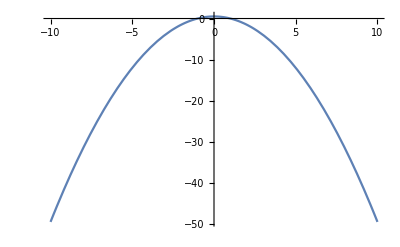

```mathematica
Plot[Integrate[-K,{K,1,x}],{x,-10,10}]
```

Therefore, terms with ⅇ^(-Integrate[-m[K[1]],{K[1],1,x}) should not apper, since it diverge at ±∞. Hence, the coefficient c1 has to be zero.
In this case the answer is simply:

```mathematica
\psi_1 (x,y)&=e^{\text{Int}(x)} C(y) \\
    \psi_2 (x,y)&=-i\psi_1(x,y)
```

Assuming m(x)=-x

Then,  terms with ⅇ^(Integrate[-m[K[1]],{K[1],1,x}) should not apper. Hence, calculation shows the condition C_1=-ⅇC_2 gives the expected (non-divegent) result:

```mathematica
\psi_1 (x,y)&=e^{-\text{Int}(x)} C(y) \\
    \psi_2 (x,y)&=i\psi_1(x,y)
```